#### 1)

```mathematica
f=5/x^3-4/((x^7)^(1/4));
g=Sin[x]/Log[x];
h=Tan[3x]Exp[x^3];
D[f,x]
D[g,x]
D[h,x]
```

-15/x^4+(7 x^6)/((x^7)^(5/4))

Cos[x]/Log[x]-Sin[x]/(x Log[x]^2)

3 ⅇ^(x^3) Sec[3 x]^2+3 ⅇ^(x^3) x^2 Tan[3 x]

#### 2)

-6 x-3 x^2+8 x^3+6 x^4

-6-6 x+24 x^2+24 x^3

{{x→-1},{x→-1/2},{x→1/2}}

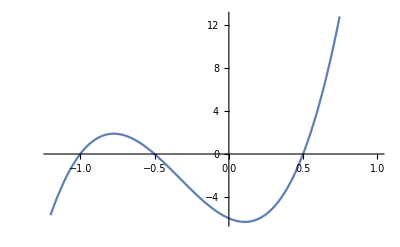

6 x^4+8 x^3-3 x^2-6 x

```mathematica
(x+1)(2x-1)(2x+1)//Expand;
Integrate[%,x]6//Expand
%//TeXForm
D[%,x]
Solve[%==0,x]
Plot[%%,{x,-1.2,1}]
```

#### 3)

```mathematica
(2-5I)/(5+2I)+I^28
(z-3+2I)(z-3-2I)//Expand
```

1-ⅈ

13-6 z+z^2

#### 4)

```mathematica
3/(x+2)+4/(x-3)//Together
Numerator[%]/Expand[Denominator[%]]
Integrate[%,x]
%%//TeXForm
```

(-1+7 x)/((-3+x) (2+x))

(-1+7 x)/(-6-x+x^2)

4 Log[3-x]+3 Log[2+x]

\frac{7 x-1}{x^2-x-6}

#### 5)

2-3 x+x^2

{{x→1},{x→2}}

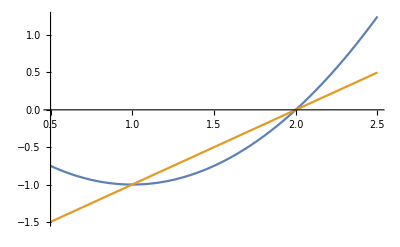

1/6

```mathematica
(x-1)(x-2)//Expand
y1=x^2-2x;
y2=x-2;
Solve[y1==y2,x]
Plot[{y1,y2},{x,0.5,2.5}]
Integrate[y2-y1,{x,1,2}]
```

#### 6)

```mathematica
A1={{1,2,-1},{2,3,-1},{-3,2,1}}
X1={1,0,2};
B1=A1.X1
```

{{1,2,-1},{2,3,-1},{-3,2,1}}

{-1,0,-1}

#### 7)

1

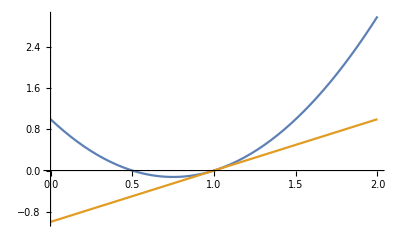

-1+x

```mathematica
f1[x_]:=2 x^2-3x+1;
f1'[1]
g1[x_]:=x-1+f1[1];
Plot[{f1[x],g1[x]},{x,0,2}]
g1[x]
```

#### 8)

```mathematica
y1=x^2;
y2=2x;
S=Integrate[(y2-y1),{x,0,2}]
Sy=Integrate[(y2-y1)x,{x,0,2}]
Sx=1/2Integrate[y2^2-y1^2,{x,0,2}]
```

4/3

4/3

32/15